## Green function for vector metric perturbation in AdS_5 Vaidya

#### Order in future time upto which the Green function is evaluated

```mathematica
i=3500;
```

### Input parameters and assumptions

t = -t_1, and t_1< 0 is the past time, used in the text.

```mathematica
t=5.0;
k=1.1;
```

```mathematica
$Assumptions=And[z∈Reals,z≥0,z≤1,ω∈Reals];
```

### Series expansion of the coefficient of z^(Δ_+)of the v < 0 solution,

lstJ lists the (J̃)_n

```mathematica
lstJ=CoefficientList[Series[(k Sqrt[t^2+2 t z])^(-3/2) BesselJ[-3/2,k Sqrt[t^2+2 t z]],{z,0,1}],z];
Do[AppendTo[lstJ,-((2 (l-1) (l-1+3/2) lstJ[[l]]+k^2 t lstJ[[l-1]])/(t l (l-1)))],{l,2,i}];
```

### Series expansion of the coefficient of z^(Δ_+)of the v > 0 solution,

a[ l ] are arrays which list a_n^j

```mathematica
a[j_]:={};
a[0]={1};
a[1]={0,-I};
a[2]={k^2/8,0,(-5 I a[1][[2]])/8};
a[3]={0,(k^2 a[1][[2]]-7 I a[2][[1]])/15,0,(-7 I a[2][[3]])/15};
For[l=4,l≤i,l++,AppendTo[a[l],(k^2 a[l-2][[1]]+((l-1)^2-9) a[l-4][[1]])/(l (l+2))];
For[j=2,j≤l-3,j++,AppendTo[a[l],(-I (2 l+1) a[l-1][[j-1]]+k^2 a[l-2][[j]]+((l-1)^2-9) a[l-4][[j]])/(l (l+2))]];
For[j=l-2,j≤l-1,j++,AppendTo[a[l],(-I (2 l+1) a[l-1][[j-1]]+k^2 a[l-2][[j]])/(l (l+2))]];
For[j=l,j≤l+1,j++,AppendTo[a[l],(-I (2 l+1) a[l-1][[j-1]])/(l (l+2))]]]
```

### Moments, M, are calculated using eq. (2.14) and (2.15)

```mathematica
M=ConstantArray[lstJ[[1]],1];
For[j=2,j≤i+1,j++,AppendTo[M,1/a[j-1][[j]] (lstJ[[j]]-Sum[M[[l]] a[j-1][[l]],{l,1,j-1}])]];
```

### The thermalizing Green function of eq. (2.18) is constructed Pade Approximation is used

```mathematica
G[x_]=-2 2^(-1/2) Sqrt[π] k^3 PadeApproximant[Sum[(-I x)^l/l! M[[l+1]],{l,0,i}],{x,0,{i/2-1,i/2+1}}];
```

### Vacuum Green function

```mathematica
Gvac[x_]=-2 2^(-1/2) Sqrt[π] (k/(x+t))^(3/2) BesselJ[-3/2,k (x+t)];
```

### Plot of figure 6

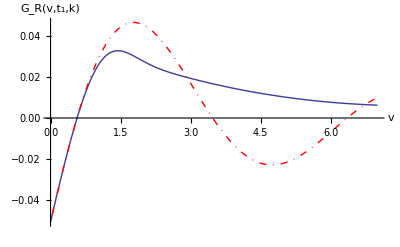

```mathematica
Plot[{G[x],Gvac[x]},{x,0,7},PlotRange->Full,PlotStyle->{Thick,{Thick,DotDashed,Red}},AxesLabel->{Style["v",FontSize->16],Style["\!\(\*SubscriptBox[\(G\),\(R\)]\)(v,\!\(\*SubscriptBox[\(t\),\(1\)]\),k)",FontSize->16]}]
```

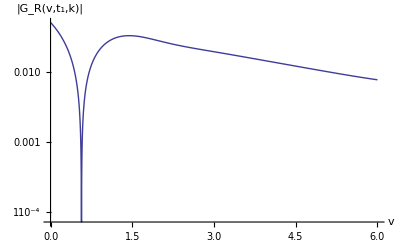

```mathematica
LogPlot[{Abs[G[x]]},{x,0,6},PlotRange->Full,PlotStyle->Thick,AxesLabel->{Style["v",FontSize->16],Style["|\!\(\*SubscriptBox[\(G\),\(R\)]\)(v,\!\(\*SubscriptBox[\(t\),\(1\)]\),k)|",FontSize->16]}]
```